## Maria José Dominguez Mesa

# OSCILADORES BIOLÓGICOS

La sincronización se ha observado en sistemas de diferente naturaleza, como circuitos electrónicos, reacciones químicas y sistemas biológicos y ecológicos, este fenómeno se puede ver como un ajuste de las frecuencias de varios osciladores, los cuales llegan a una frecuencia o ritmo uniforme a pesar de que las frecuencias intrínsecas de cada individuo sean distintas.
En ausencia de un oscilador lider que actue como marcapasos externo para el sistema se tienen dos categorías de ritmicidad:

	⋄cuando los individuos no tienen ritmicidad intrínseca pero en conjunto sí (hormigas leptothorax)
	⋄cuando los individuos presentan ritmicidad intrínseca y en grupo crean un patrón (estridulación de grillos, respiración de las abejas,etc)
	
Este último es el caso de la sincronización de los destellos de las luciérnagas. Cada luciérnaga oscila con una frecuencia natural carácterística en ausencia de estímulos, la cual cambia en la presencia de luciérnagas vecinas al ver los destellos de ellas, se tiene entonces que la sincronización es global y creciente en el tiempo. Cuando el estímulo llega antes de el destello propio la luciérnaga aumenta su frecuencia en un intento de igualar la frecuencia del estímulo, a su vez, si viene después de su destello la disminuye.

Modelo para dos luciérnagas (Ermentrout y Rinzel -1984)

 Suponiendo que la fase de los destellos de una luciernaga está dada por θ(t), donde θ=0 corresponde al instante en el cual se emite el flash de luz y la cual cumple con la ecuación θ̇= ω cuando no hay estímulos externos presentes y suponiendo también un estímulo periódico (otra luciérnaga) cuya fase está dada por Θ(t), y donde Θ=0 corresponde al momento en el que emite luz y que cumple la ecuación Θ̇=Ω. Se tiene entonces que:
 	
 	θ̇= ω+Ksen(Θ-θ)
 	
 Donde K>0, el cual mide la habilidad de la luciérnaga de cambiar su frecuencia instantánea, y por tanto de sincronizarse al estímulo.
 
 Para ver si el entrelazamiento es posible de debe analizar la dinámica del cambio de fase ϕ= Θ-θ, derivando respecto al tiempo y teniendo en cuenta las ecuaciones anteriores para θ̇ y Θ̇ se tiene que:
 
 	ϕ̇= Ω- ω-Ksen(ϕ)
 	
 ⋄Adimensionalización:
 
 Definiendo τ=Kt y μ= (Ω-ω)/K podemos crear una nueva ecuación adimensional, donde μ es una medida de las frecuencias relativas:
 
 	dϕ/dτ=μ-sen(ϕ)

```mathematica
eq1= {ϕ'[τ]== μ-Sin[ϕ[τ]]};
var1= {ϕ[τ]};
Manipulate[Show[Plot[μ-Sin[ϕ], {ϕ,-π,π}, Frame->True,PlotLegends->{"ϕ'(τ)=μ-Sin(ϕ(τ))"},AxesLabel->{"ϕ","ϕ̇"},PlotRange->{-3,3}],VectorPlot[{Sign[μ-Sin[ϕ]],0}, {ϕ,-π,π},{y,-10,10},VectorStyle->{Gray,"Arrow"},VectorScale->0.02, RegionFunction->Function[{x,y,vx,vy,n}, -1<y<1] ]],{μ,0,2}]
```

Para μ=0 se tiene que ambas frecuencias son iguales, por esto hay sincronización perfecta, se presenta un punto fijo estable ϕ*=0

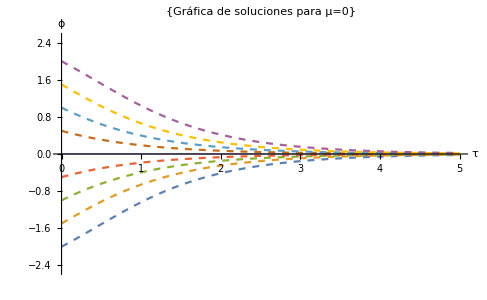

```mathematica
s1=NDSolve[{ϕ'[τ]== μ-Sin[ϕ[τ]]/.{K-> 2, μ-> 0}, ϕ[0]==c1}, ϕ[τ], {τ,0,20}]
Plot[Evaluate[ϕ[τ]/.s1/.{{c1->-2},{c1-> -1.5},{c1-> -1},{c1->-0.5},{c1-> 0},{c1->0.5},{c1-> 1},{c1-> 1.5},{c1-> 2}}], {τ,0,5}, PlotRange->{-2.5,2.5}, PlotLabel->{"Gráfica de soluciones para μ=0"},PlotStyle->{Dashed, Dashed,Dashed,Dashed,Thick, Dashed, Dashed, Dashed,Dashed},AxesLabel->{"τ","ϕ"}]
```

Para 0<μ<1 se sigue teniendo sincronización, ambos osciladores presentan la misma frecuencia instantánea pero ya con fases diferentes, por lo cual el destello no ocurre en el mismo instante. La diferencia de fase tiende a una constante equivalente al punto fijo estable ϕ*=c, esta situación se conoce como phase-locking.
En la gráfica se observa el punto fijo ϕ*= π/6 obtenido con un valor de μ=0.5.

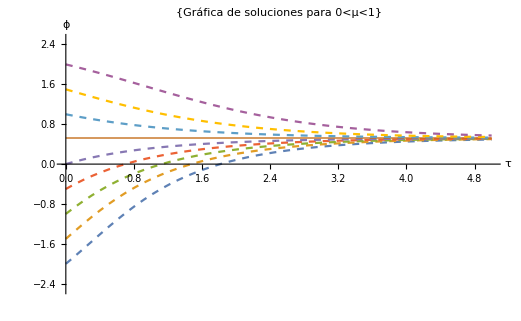

```mathematica
s2=NDSolve[{ϕ'[τ]== μ-Sin[ϕ[τ]]/.{K-> 2, μ-> 0.5}, ϕ[0]==c2}, ϕ[τ], {τ,0,20}]
Plot[Evaluate[ϕ[τ]/.s2/.{{c2->-2},{c2-> -1.5},{c2-> -1},{c2->-0.5},{c2-> 0},{c2->π/6},{c2-> 1},{c2-> 1.5},{c2-> 2}}], {τ,0,5}, PlotRange->{-2.5,2.5}, PlotLabel->{"Gráfica de soluciones para 0<μ<1"},PlotStyle->{Dashed, Dashed,Dashed,Dashed, Dashed,Thick, Dashed, Dashed,Dashed},AxesLabel->{"τ","ϕ"}]
```

Para μ=1 se tiene una situación crítica de sincronización, donde el punto fijo se convierte en un punto de silla, comportándose como un punto fijo estable para valores negativos y un punto inestable para valores positivos.
En la gráfica se observa el punto fijo ϕ*= π/2.

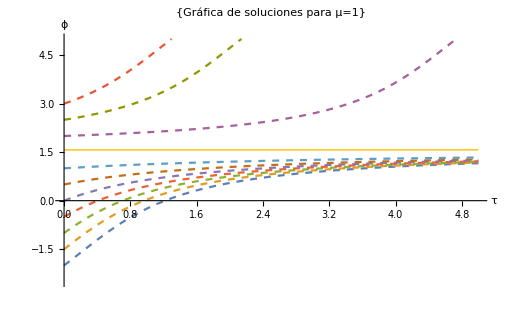

```mathematica
s3=NDSolve[{ϕ'[τ]== μ-Sin[ϕ[τ]]/.{K-> 2, μ-> 1}, ϕ[0]==c3}, ϕ[τ], {τ,0,20}]
Plot[Evaluate[ϕ[τ]/.s3/.{{c3->-2},{c3-> -1.5},{c3-> -1},{c3->-0.5},{c3-> 0},{c3->0.5},{c3-> 1},{c3-> π/2},{c3-> 2},{c3-> 2.5},{c3-> 3}}], {τ,0,5}, PlotRange->{-2.5,5}, PlotLabel->{"Gráfica de soluciones para μ=1"},PlotStyle->{Dashed, Dashed,Dashed,Dashed, Dashed, Dashed, Dashed,Thick,Dashed, Dashed, Dashed},AxesLabel->{"τ","ϕ"}]
```

Para μ>1 se pierde la sincronización, esto se manifiesta con una ausencia de puntos fijos, pero la luciérnaga sigue intentando en vano sincronizarse con el estímulo, aumentando y disminuyendo constantemente su frecuencia hasta que se completa el ciclo en ϕ=2π, la rata de separación de las fases no es entonces constante, ϕ crece más lentamente cuando pasa por ϕ= nπ/2 lo cual tiene sentido pues es el mínimo de la función seno, y más rápidamente por ϕ= -nπ/2, valor que corresponde al máximo. Esta situación situación se conoce como phase-drift. El tiempo para que el sistema complete un ciclo se define como T_drift= (2π)/(√((Ω-ω)^2-K^2)).

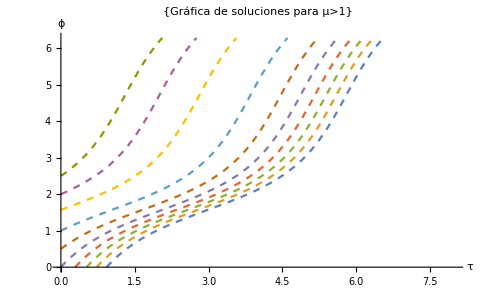

```mathematica
s4=NDSolve[{ϕ'[τ]== μ-Sin[ϕ[τ]]/.{K-> 2, μ-> 1.5}, ϕ[0]==c3}, ϕ[τ], {τ,0,20}]
Plot[Evaluate[ϕ[τ]/.s4/.{{c3->-2},{c3-> -1.5},{c3-> -1},{c3->-0.5},{c3-> 0},{c3->0.5},{c3-> 1},{c3-> π/2},{c3-> 2},{c3-> 2.5}}], {τ,0,8}, PlotRange->{0,2π}, PlotLabel->{"Gráfica de soluciones para μ>1"},PlotStyle->{Dashed, Dashed,Dashed,Dashed, Dashed, Dashed, Dashed,Dashed,Dashed, Dashed},AxesLabel->{"τ","ϕ"}]
```

En general, para que ocurra el entrelazamiento el sistema debe presentar puntos fijos, por lo tanto se debe cumplir que:

	Ω- ω-Ksen(ϕ)=0 ⇒ sen(ϕ)= (Ω- ω)/K
como -1≤sen(ϕ)≤1 se sigue que:
-1≤(Ω- ω)/K≤1 ⇒ ω-K≤Ω≤ω+K
el cual se define como el rango de entrelazamiento.

Modelo de Kuramoto (para N luciérnagas)

El modelo de Kuramoto consiste en una población de N osciladores acoplados de fase θ_i(t) y cuyas frecuencias naturales ω_i están distribuidas con una probabilidad de densidad g(ω), cada oscilador trata de actuar de manera independiente con su propia frecuencia, mientras que el acoplamiento lo tiende a sincronizar con los demás. La dinámica del sistema se rige por:

	(θ̇)_i= ω_i+ K/N∑_(j=1)^N sen(θ_j-θ_i) ,  i=1,2,...,N
	
Donde K sigue siendo el factor de acoplamiento y la división por N asegura un buen comportamiento del sistema cuando N→∞. Por simplicidad se elige que la distribución sea de tipo gaussiana, es decir, simétrica respecto a la frecuencia media Ω y unimodal, además, gracias a la simetría rotacional del sistema de puede elegir Ω=0 redefiniendo θ_i →θ_i+Ωt, se tiene entonces que ω_i denota la desviación de la frecuencia media Ω.

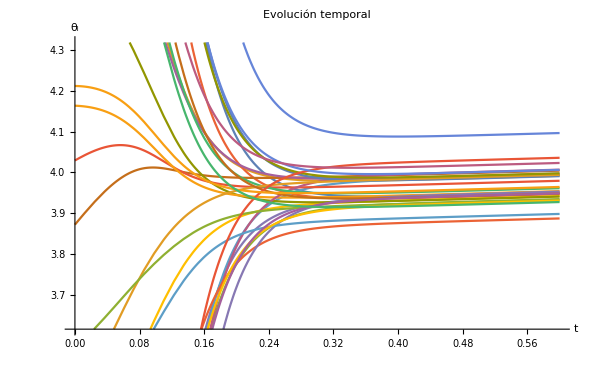

```mathematica
n=30;
k=25;
eqns=Table[θ[i]'[t]==RandomVariate[NormalDistribution[0,1]]+(k/n)*Sum[Sin[θ[j][t]-θ[i][t]],{j,1,n}],{i,1,n}]
sol=NDSolve[{eqns,Table[θ[i][0]==RandomReal[{1,2π}],{i,1,n}]},Table[θ[i][t],{i,1,n}],{t,0,5000}]
Plot[Evaluate[Table[θ[i][t],{i,1,n}]/.sol],{t,0,0.6},PlotLabel->"Evolución temporal",AxesLabel->{Style["t"],Style["θ_i"]}]
```

Para visualizar la dinámica de las fases es conveniente considerar el ritmo colectivo del sistema, o el punto central de las fases de los osciladores visto en el plano complejo, para esto definimos dicho ritmo colectivo como el parámetro de orden complejo siguiente:

	rⅇ^iψ= 1/N∑_(j=1)^N ⅇ^iθ_j
	
Donde el radio mide la coherencia de fase(o la media de los módulos de todas las posiciones) y ψ(t) es la fase promedio. Kuramoto descubrió que la ecuación gobernante del sistema se puede escribir en términos del parámetro de orden multiplicándolo en ambos lados por ⅇ^-iθ_i, obteniendo:

	rⅇ^(i(ψ-θ_i))= 1/N∑_(j=1)^N ⅇ^(i(θ_j-θ_i))
	
cuya parte imaginaria conlleva a:

	rsen(ψ-θ_i)=1/N∑_(j=1)^N sen(θ_j-θ_i) 
	
Lo cual hace que la ecuación del sistema tome la forma:

	(θ̇)_i= ω_i+ Krsen(ψ-θ_i) ,  i=1,2,...,N

Aunque en esta ecuación cada oscilador parezca desacoplado de los demás, se sigue teniendo interacción, pero solo a través de los valores medios de la coherencia y la fase. Se tiene entonces que las fases θ_i son atraídas hacia la fase media ψ, en vez de atraerse entre sí individualmente, además, la capacidad de acoplamiento es proporcional a r, mientras la población se vuelve más coherente r crece, y se sigue que K crece, lo cual aumenta el “reclutamiento” de más individuos.

```mathematica
Manipulate[Block[{θsols,θords},θsols={Table[Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol1][[1,i]],{i,1,Nosc}],Table[Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol2][[1,i]],{i,1,Nosc}],Table[Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol3][[1,i]],{i,1,Nosc}],Table[Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol4][[1,i]],{i,1,Nosc}]};θords={(1/Nosc)*Sum[Exp[ⅈ*Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol1][[1,i]]],{i,1,Nosc}],(1/Nosc)*Sum[Exp[ⅈ*Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol2][[1,i]]],{i,1,Nosc}],(1/Nosc)*Sum[Exp[ⅈ*Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol3][[1,i]]],{i,1,Nosc}],(1/Nosc)*Sum[Exp[ⅈ*Evaluate[Table[θ[i][t],{i,1,Nosc,1}]/.sol4][[1,i]]],{i,1,Nosc}]};Show[{Graphics[{
Style[Text[StringJoin[{
ToString[TraditionalForm[r]]," = ",
ToString[Abs@θords[[k]]]}],{0,0}],{Black,18}],Circle[{0,0},1]}],
ListPlot[Transpose[{Cos/@θsols[[k]],Sin/@θsols[[k]]}],
Frame-> Off,AspectRatio-> 1,PlotStyle->{Darker@Purple,PointSize[0.025]},PlotRange->{{-1,1},{-1,1}}]
},ImageSize-> {450,450}]],
{{k,3,"Parámetro de acoplamiento"},
{1-> Row[{Style["K",Italic]," = 0.05"}],
2->Row[{Style["K",Italic]," = ",Subscript[Style["K",Italic],Style["C",Plain]]," = 0.1"}],
3-> Row[{Style["K",Italic]," = 0.25"}],
4-> Row[{Style["K",Italic]," = 0.5"}]
},Setter},
{{t,0,"tiempo"},0,tmax,10,Appearance->"Labeled"},
TrackedSymbols:>{t,k},ControlPlacement->Top,
Initialization:>(
Nosc=35;
tmax=10000;
SeedRandom[Nosc];
gammadisp=0.05;
omegadata=RandomVariate[NormalDistribution[0.,gammadisp],Nosc];
Kcoupl1=0.05;Kcoupl2=2*gammadisp;Kcoupl3=0.25;Kcoupl4=0.5; 
       θstart=RandomReal[{0,2*Pi},Nosc];
eqns1={Table[θ[i]'[tt]==omegadata[[i]]+Kcoupl1/Nosc*Sum[Sin[θ[j][tt]-θ[i][tt]],{j,1,Nosc,1}],{i,1,Nosc,1}],Table[θ[i][0]==θstart[[i]],{i,1,Nosc,1}]};
sol1=NDSolve[eqns1,Table[θ[i],{i,1,Nosc,1}],{tt,0,tmax,1}];
eqns2={Table[θ[i]'[tt]==omegadata[[i]]+Kcoupl2/Nosc*Sum[Sin[θ[j][tt]-θ[i][tt]],{j,1,Nosc,1}],{i,1,Nosc,1}],Table[θ[i][0]==θstart[[i]],{i,1,Nosc,1}]};
sol2=NDSolve[eqns2,Table[θ[i],{i,1,Nosc,1}],{tt,0,tmax,1}];
eqns3={Table[θ[i]'[tt]==omegadata[[i]]+Kcoupl3/Nosc*Sum[Sin[θ[j][tt]-θ[i][tt]],{j,1,Nosc,1}],{i,1,Nosc,1}],Table[θ[i][0]==θstart[[i]],{i,1,Nosc,1}]};
sol3=NDSolve[eqns3,Table[θ[i],{i,1,Nosc,1}],{tt,0,tmax,1}];eqns4={Table[θ[i]'[tt]==omegadata[[i]]+Kcoupl4/Nosc*Sum[Sin[θ[j][tt]-θ[i][tt]],{j,1,Nosc,1}],{i,1,Nosc,1}],Table[θ[i][0]==θstart[[i]],{i,1,Nosc,1}]};
sol4=NDSolve[eqns4,Table[θ[i],{i,1,Nosc,1}],{tt,0,tmax,1}];)]
```

Al variar el factor de acoplamiento K notamos que para los valores por debajo del valor crítico K_c el estado es incoherente y los osciladores actuan como si no estuvieran acoplados, notorio por la distribución uniforme en el círculo, mientras que cuando el factor supera el valor crítico se comienza a haber sincronía, la cual aumenta proporcionalmente a medida que K aumenta, aunque se pueden apreciar aún ciertos individuos desacoplados.

### Referencias

⋄Strogatz, S. H. Nonlinear Dynamics and Chaos, with Applications to Physics, Biology,
Chemistry, and Engineering. Reading, MA: Addison-Wesley, 1994.
	⋄Strogatz, S. H.From Kuramoto to Crawford: explorative the onset of synchronization in populations of coupled oscillators.Physica D: Nonlinear Phenomena. 2000. https://doi.org/10.1016/S0167-2789(00)00094-4
	⋄Marsh, J. The Kuramoto Model: A presentation in partial satisfaction of the requirements for the degree of MSc in Applied Mathematics.University of Colorado. 2008. https://www.uccs.edu/~jmarsh2/doc/Kuramoto.pdf